# Mathematica Live-Coding Training for Physical Chemistry Labs

Dr. Jefferson E. Bates
Fall 2024

Your Name Here

As a part of your Physical Chemistry education, you will be learning a new Language: Mathematica. This programming language is very powerful and flexible once you get over the initial learning curve. This notebook is designed to help give you a logical flow for learning the key components you will need to excel at data analysis and in your lecture homework.

First steps. You are able to type many Greek and Mathematical symbols using the “Esc” key on your keyboard. For instance, if you want the character π, you need to type the following sequence: 
Esc key
pi
Esc key
If done correctly you should see the π symbol appear. Evaluate the cell to see that it is assigned the correct value.
Aside: The Greek alphabet is mapped closely to the English alphabet so characters such as : a ⟶ α, b ⟶ β, etc. Give it a try. 
NOTE : π is special and assigned a value by Mathematica. The other letters  are NOT automatically mapped to numerical values.

```mathematica
α (* this is an example of a comment as well, if you wish to teach your students about comments*)
γ
```

Note: if you wish to extract a numerical value from a constant or expression, use the “N” function in one of two ways: i) using it as a Mathematica Function N[ ... ] , or as a modifier after the expression has been created //N.

```mathematica
π
N[π]
π//N
```

π

3.14159

3.14159

## Math Operations

### Algebra

Mathematica is a very fancy calculator. It can absolutely perform all of the basic mathematics you are used to performing with a calculator or spreadsheet. It can also store variables so that you can make the equations in Mathematica look like ones from textbooks or lecture notes. Below are some examples from general chemistry.

Note also that capital letters are distinguished from lowercase in Mathematica, so HOW you SPELL variables and functions REALLY matters. This is especially true when calling functions, which will be discussed more below.

#### Example: Convert moles to atoms for water

NOTE: DO NOT USE A “E” CHARACTER AS A SHORTCUT FOR “x10^”. In Mathematica, “E” is a short cut to “e” the exponential number/function. You should ALWAYS use “ *10^(power) ” to ensure your exponents are done correctly.

Given 1.5 moles of water, how many molecules does this correspond to? We can save the result as Nmolecules in case we need it later.

```mathematica
Nmolecules = 1.5 * 6.022*10^(23)
```

9.033×10^23

#### Check for Understanding I: Convert molecules water to atoms H

Instructions:
Since the chemical formula for water is H_2O, as chemists we know that there are two atoms of H per molecule of water. So if we want to convert the answer from molecules of water to atoms of hydrogen, what would you do? You must use Nmolecules in your answer! Save the result as Nhydrogen.

```mathematica
Nhydrogen=Nmolecules*2
```

1.8066×10^24

#### Example: Calculate Gibbs Free Energy of Formation

Let’s calculate the Gibb’s free energy of formation for iron(II) chloride. If you were using excel or your calculator, you would punch the numbers in according to the formula below, and out comes the result. 
ΔG_0(T) = ΔH_0 - T * ΔS_0
Mathematica can help us save the value of ΔG_0 using the idea of variables we just discussed above. Here are the enthalpy and entropy values in reasonable units. 
ΔH_0=-341.8 kJ/mol
ΔS_0 = 117.9  J/(mol K)

Let’s use the numerical values of ΔH_0 and ΔS_0 to calculate ΔG_0 at 298 Kelvin, just like you would have done in your calculator or spreadsheet. Use the variable name deltaG298K to store the numerical value of ΔG_0(298 K).

Note that it is BEST to put a “*” between things you wish to MULTIPLY and a “/” between things you wish to divide. Use parentheses to make double sure you get what you want.

```mathematica
deltaG298K = -341.8 - (298)*(117.9 / 1000)
```

-376.934

#### Caveat: A few words on Mathematica Syntax

A few words on Mathematica Syntax:
You will have to use functions  to calculate exponentials, logs, trig functions, etc in Mathematica. These functions always use square brackets, [ ], to open and close the arguments. This is analogous to your mathematics class where soft parentheses ( ) were used to indicate the arguments. So if f(x) was your function in math class, f[x] is your function in Mathematica. Native Mathematica functions always begin with a capital letter. For instance, if you wanted to take the log_10 (log base 10) of 10^3.5, or the exponential of 2.5, or the natural log of 10.5:

Math Class | Mathematica
log_10(10^3.5) | Log10[10^3.5]
e^2.5
ln(10.5) | Exp[2.5]
Log[ 10.5 ]
cos(x) | Cos[x]

#### Example: Calculate the Equilibrium Constant from ΔG

Now that we have calculated ΔG_0(298K) for FeCl_2, we can use the result to calculate other useful chemical information. Let’s calculate the equilibrium constant K = Exp[-ΔG_0 / R T] @ 298 K .

Take the exponential of -deltaGRT/( R * T) and save the result as a variable called KeqFeCl2. The exponential function is Exp[ ] in Mathematica. You will need to replace R and T with values, watch units!
Does the equilibrium favor reactants or products for the formation of iron(II) chloride?

```mathematica
KeqFeCl2=Exp[-deltaG298K/(8.314/1000 * 298)]
```

1.18285×10^66

Formation of the products is heavily favored for iron(ii) chloride.

### Variable Substitutions ⟵ the true power of Mathematica!

The true power of Mathematica lies in the ability to assign variables without numerical values inside of expressions. You are then able to make small changes to an substitution rule in order to obtain different values. This is similar to using the “A1 + B1”  syntax in a spreadsheet formula which can then be applied to multiple cells. In Mathematica, any word that appears as blue in an evaluation cell is considered an unassigned variable and can be substituted at a later time when constructing an expression.  

The underlying syntax looks like this: 
expression /. vairable ⟶ value 
The use of “/.” tells Mathematica to substitute the variable with the provided value. Let’s walk through an example together, and then test your skills. Note the color coding is designed to help you keep track of what has and has not been assigned a numerical value.

#### Example: Calculating total pressure in a carboy P_(1,tot)

In one of the experiments for this semester, you will measure the pressure of a carboy vessel using a manometer. This instrument enables you to measure the relative pressure (ΔP) of the carboy vessel compared to the atmospheric pressure (P_2). We will use a digital manometer for this task, which has a display screen for the  pressure reading. In order to calculate the total pressure in the carboy once it has been filled with gas, we have to add the pressure of the carboy to the atmospheric pressure. 
-Graphics-
If we make a general expression for this concept, then we can use variable substitution to evaluate the total pressure for any values of the atmospheric and carboy pressures.

Create an expression called Ptot that involves the two variables P2 and ΔP according to the equation above. P2 and ΔP should both be blue! We will use this expression to calculate the total pressures, p1tot and p3tot.

```mathematica
Ptot = P2 + ΔP
```

P2+ΔP

How do you actually substitute a value for P2 and ΔP then? In Mathematica we use the following syntax:
p1tot = Ptot/. variable1 -> value1 /.variable2 -> variable2
Note the use of “slash dot”, note this is a forward slash, followed by a period, then the variable name, a “minus sign”, “a greater than sign”, a space (which will cause the arrow to form), and then the value to be substituted. This pattern can be repeated multiple times in order to substitute multiple variables with numerical values.

For a particular experiment, you measure the atmospheric pressure to be P_2 = 867.66 hPa and the manometer indicates the pressure in the carboy is ΔP = 74.2 hPa. Use substitution to calculate the value of p1tot based on these measurements.

```mathematica
p1tot=Ptot/.P2->867.66/.ΔP->74.2
```

941.86

#### Check for Understanding I: Calculating total carboy pressure P_(3,tot)

After “burping” the carboy, the pressure inside will decrease forming the basis of P_3 for the heat capacity ratio experiment. Check your understanding of substitution by following the instructions below.

Instructions: 
1. Using your expression for Ptot, calculate the total pressure for state P3 if P2 = 867.66 hPa and ΔP = 28.2 hPa. Store this result in the variable p3tot

```mathematica
p3tot=Ptot/.P2->867.66/.ΔP->28.2
```

895.86

#### Example: Calculate the heat capacity ratio of an ideal gas, γ

In one of our experiments you will calculate the heat capacity ratio of two ideal gasses. In order to do this you will utilize the following equation that involves three total pressures: 
γ= Ln[P_1/P_2]/Ln[P_1/P_3]
Let’s use our total pressures from the previous calculations to calculate the heat capacity ratio.

First, create an expression called heatcapratio that depends on the symbols P1, P2, & P3. Don’t forget that the natural log in Mathematica is Log[x], there is no Ln function!

```mathematica
heatcapacityratio=Log[P1/P2]/Log[P1/P3]
```

Log[P1/P2]/Log[P1/P3]

Using your expression, calculate the heat capacity ratio (γ), by substituting p1tot, p3tot for P1 and P3, and substituting P2 = 867.66 hPa. Your value should be between 1 and 2. Store the result in the expression γ1.

```mathematica
γ1=heatcapacityratio/.P1->p1tot/.P2->867.66/.P3->p3tot
```

1.63876

#### Example: Calculate the relative error propagation for heat capacity ratio, Δγ

We will be continuing to use the relative error propagation method encountered in your previous courses in order to estimate uncertainties for quantities in this course. Recall that for a function f(x,y,z) with three independent variables, x, y, & z, the relative error can be calculated according to the equations:
-Graphics-
where the first is the relative error divided by the function value, and the second equation is directly the equation for the relative uncertainty. Let’s calculate the relative error of our heat capacity ratio from the previous cells using substitution!

Follow along with your instructor to build up this expression. Use the name deltaγ for your uncertainty, and build an expression that depends on P1, P2, and P3, similarly to what was done above for the heat capacity ratio, as well as ΔP1, ΔP2, & ΔP3. The equation you are building replaces x, y, & z with P1, P2, & P3. f in this example will be γ1 that you’ve already built above.

```mathematica
deltaγ=γ*Sqrt[(ΔP1/P1)^2+(ΔP2/P2)^2+(ΔP3/P3)^2]
```

γ √(ΔP1^2/P1^2+ΔP2^2/P2^2+ΔP3^2/P3^2)

Once you have your expression for deltaγ, use substitution to replace ΔP1 = 0.35 hPa, ΔP2 = 0.25 hPa, and ΔP3 = 0.40 cm Hg. Plug in the values for P1, P2, and P3 used to calculate the heat capacity ratio above using substitution, as well as γ1 for γ.

```mathematica
Δγ1=deltaγ/.γ->γ1/.P1->p1tot/.P2->867.66/.P3->p3tot/.ΔP1->0.35/.ΔP2->0.25/.ΔP3->0.40
```

0.00106263

#### Example: Using the Solve function to obtain Pressure of van der Waals gas

Often in Physical Chemistry we will be given an equation, or system of equations, and asked to solve for some unknown variables. Mathematica can tackle this type of problem through the solve function and substitution rules!

Consider the equation of state for a van der Waals gas: 
(P+a n^2/V^2)(V - n b) = n R T

This equation is the generalization of the ideal gas equation, PV = nRT, but for a non-ideal gas described with van der Waals dispersion forces. Solving for the pressure in this equation is now no longer trivial. Use the Solve function to obtain the pressure, P, as a function of (V, n, R, T). 
Tips: Remember to replace the equal sign in a Solve function w/ DOUBLE equal signs in Mathematica!  
Solve[ y == m*x + b, x] ⟵ this example would solve the equation for x.

```mathematica
psolve=Solve[(P+a*(n/V)^2)(V - n*b)== n* R * T, P]
```

{{P→(a b n^3-a n^2 V+n R T V^2)/(V^2 (-b n+V))}}

### Calculus in Mathematica: Derivatives and Integrals

Common calculus operations are another big feature of Mathematica that you will use in your lab and lecture course. The calculation of Derivative-based Errors involves taking partial derivatives of multivariable functions, so it is most important to get the derivative down from this set of exercises if your instructor utilizes a derivative-based error propagation. Integrals and derivatives also arise regularly in physical chemistry lecture concepts and example problems.Taking derivatives and integrals can be as simple as one line, if you give the correct input function, variables, and potentially integration limits.

#### Example: Calculate the Derivative of a Quadratic function

Derivatives are crucial for rigorous error analysis. Understanding how they work, and why they sometimes do NOT work, will make your data analysis go much more smoothly. Let’s start by reviewing a simple derivative, that of the function below:
 f(x) =a* x^2 + b *x + c
Hopefully you can quickly work this out by hand, but now you can also ask Mathematica to do it using the “Derivative function” within Mathematica. That is, we can ask Mathematica to do the following: 
(∂f(x))/(∂x) 
once you understand the syntax.

Before we can take a derivative, we need to assign an EXPRESSION to take a derivative OF. 
Name your expression express1, as it will be reused in several places below. 
NOTE : you must use SPACES or multiplication symbols, *, BETWEEN characters such as “a” and “x” otherwise Mathematica will treat them as ONE variable “ax”.

```mathematica
express1 = a*x^2+b*x+c
```

c+b x+a x^2

To take the derivative of express1 we use the “D” function, and specify the variable as the second argument separated by a comma. Let’s save the result as dexpress1 incase we need it later. Take the derivative by hand, do you get the same result?

```mathematica
dexpress1=D[express1,x]
```

b+2 a x

#### Check for Understanding I: Calculate the Heat Capacity of a monatomic Ideal Gas

The internal energy of a monatomic ideal gas can be described by the mathematical function:
U(T) = 3/2 R T
where R is the ideal gas constant, and T is the temperature. The constant volume heat capacity of such a gas is given by the partial derivative:
C_v = ((∂U(T))/(∂T))_V 
which is to take a derivative of U with respect to T, while keeping V fixed. Follow the instructions below to explore this concept with your new skills.

Instructions: 
1. Create a new expression for the energy called Umonatom, and set it equal to 3/2 Rgas TK. NOTE YOU MUST USE “*” or include a SPACE between Rgas & TK for Mathematica to treat them like separate quantities, otherwise Mathematica assumes you mean “RgasTK”, a single variable. 
2. Take a derivative of the expression Umonatom with respect to TK and save the result as Cvmonatom.
3. What are the units of the heat capacity of a monatomic ideal gas? Does the heat capacity depend on the temperature?

```mathematica
Umonatom=3/2 * (Rgas*TK)
```

(3 Rgas TK)/2

```mathematica
Cvmonatom=D[Umonatom,TK]
```

(3 Rgas)/2

The units of the heat capacity are determined by the units of the ideal gas constant, most typically J/(mol*K). The heat capacity does not depend on temperature for a monatomic ideal gas.

#### Example: When Derivatives DONT work

Often, as users who are still learning the language, you will assign a variable to a value, and then be unable to take a derivative. Look at the following syntax. 
1. an expression is created that depends on xvar.
2. the value 2 is associated with the expression xvar. 
3. a derivative of express2 produces an error since xvar is not a variable, but a value. 
If you see this syntax, this means your “variables” are NOT actually variables, but they have been assigned NUMERICAL VALUES.

```mathematica
express2=xvar ^2
```

xvar^2

```mathematica
xvar=2
```

2

```mathematica
D[express2,xvar]
```

General::ivar: 2 is not a valid variable.

∂_2 4

Use the ClearAll function to un-do these assignments. Note the color change after executing this. 
Try the derivative again and you should get something more meaningful.

```mathematica
ClearAll[xvar]
```

```mathematica
D[express2,xvar]
```

2 xvar

#### Example: Calculate the Integral of a Polynomial

In addition to derivatives, Integrals are also implemented in Mathematica. Mathematica will try many ways to evaluate  your integral, so being patient during evaluation can be important since it may take a few seconds depending on your computer’s processing power.

Before we begin, we need to create an expression for the function we are trying to integrate. Call your expression poly1 since we will use it several times below.

```mathematica
poly1=1/2*x+ 3/2*x^3-1/4*x^4
```

x/2+(3 x^3)/2-x^4/4

Let’s now try to do the integral. In this case, we could take a definite or an indefinite integral; Mathematica is capable of doing both depending on how you setup the Integrate command. Let’s start with indefinite since it is analogous to the derivative. Simply give Mathematica the input function and the integration variable, in this case that is poly1 and x, respectively. Do you get what you would expect if integrated by hand?

```mathematica
Integrate[poly1,x]
```

x^2/4+(3 x^4)/8-x^5/20

Now what about a definite integral? For this case, we have to use a special syntax, that is we must tell Mathematica more information about the integration. This is analogous to the Plot command you will see later. You must give a list of {integration variable, lower limit, upper limit}. So if I wanted to  integrate with respect to a variable “x” from -1 to 2, I would need a list such as {x, -1, 2}. Here it is in action. Remember that sometimes to get a numerical value you will need the N[ ... ] function or add //N after the expression

```mathematica
Integrate[poly1,{x,-1,2}]
Integrate[poly1,{x,-1,2}]//N
N[Integrate[poly1,{x,-1,2}]]
```

189/40

4.725

4.725

Note that you can use other variables as integration limits. For example, if you wanted to integrate the previous function between x1 and x2, you would input the following. Note the coloring: “x” is light green, and x1 and x2 are both blue!

```mathematica
Integrate[poly1,{x,x1,x2}]
```

1/2 (-x1^2/2+x2^2/2)+3/2 (-x1^4/4+x2^4/4)+1/4 (x1^5/5-x2^5/5)

#### Example: Calculate the Derivative of a Multivariate Function

In Physical Chemistry the functions we encounter for data analysis rarely involve only a single variable. This is especially true for derivative-based error analysis, where a multivariable expression is likely needed to compute the desired uncertainty. In this example, we will look at a simple polynomial and take the partial derivatives with respect to its variables in order to practice this skill.

In mathematics, we could have a function that depends on two variables, x & y. For such a function, there are 2 partial derivatives: one taking the deriv. with respect to x keeping y fixed, and vice versa. These would be denoted : 
((∂g(x,y))/(∂x))_y & ((∂g(x,y))/(∂y))_x

In Mathematica, the natural behavior of the derivative function is to take a partial derivative, so no extra work has to be done compared to the previous example. In the following, the expression g(x,y) depends on both variables.
The function we will use is the following:
g(x,y) = x^2*Sqrt[ Sin[y] ]
Follow along with your instructor to create the expression gofxy in order to practice taking partial derivatives.

```mathematica
gofxy=x^2*Sqrt[Sin[y]]
```

x^2 √Sin[y]

Now we are ready to take the partial derivative with respect to x and y. Let’s do x first, store the result as pdgdx, do you get what you expect? For y, store the result as pdgdy,  the derivative is much more complicated, which a the benefit of using Mathematica! Note the variable you are using to take a derivative with respect to should turn light green. You will use these functions below in order to learn about variable substitution.

```mathematica
pdgdx=D[gofxy,x]
```

2 x √Sin[y]

```mathematica
pdgdy=D[gofxy,y]
```

(x^2 Cos[y])/(2 √Sin[y])

#### Check for Understanding III: Calculate the Derivative of a Multivariate Function

Let’s use a different function in order to calculate the derivatives, h(x,y):
h(x,y) = 1/x*Sin[e^(-y^2)]

Instructions: 
1. Create an expression for h(x,y) called hofxy. Remember to use the Exp[...] function for the exponential!
2. Use the derivative method to calculate pdhdx & pdhdy in analogy to the function g(x,y).

```mathematica
hofxy=(1/x)*Sin[Exp[-y^2]]
```

Sin[ⅇ^(-y^2)]/x

```mathematica
pdhdx=D[hofxy,x]
```

-Sin[ⅇ^(-y^2)]/x^2

```mathematica
pdhdy=D[hofxy,y]
```

-(2 ⅇ^(-y^2) y Cos[ⅇ^(-y^2)])/x

## Other Mathematica Functionalities - Lists & Tables, Importing data, Plotting, & Nonlinear Fitting

Mathematica has a huge library of functions and functionalities that are ready to use. Detailed descriptions and examples of how to use them can all be found under the “Help ⟶ Wolfram Documentation” window. Search the concept or name of the function you want to use and usually you will want the first or second explanation. The general structure of the functions you will be expected to use such as Plot or the derivative, D, or the Import function to read in data from your computer involves specifying an input and generating some sort of output.

The basic requirement of most functions is an input argument, and the function then produces an output. This output could be a number, it could be a set of letters known as a string, or it could be something more complicated like a plot or table. In any case, you must always be conscious of the inputs, since the computer only does what you tell it to!

### Import: Loading External Data into Mathematica

For analyzing data collected during your lab experiments, you will need to be able to import data into Mathematica. The Import function will do this for us, but it can be tricky to get your file in the correct format. Mathematica is fairly flexible, and is able to import a great number of data types and file types. The BEST format to import from for your data processing will be as a “CSV” file, which stands for comma separated value file. All spreadsheet programs can generate this file type using the “Save As” option. Other formats are possible, please check the documentation of the Import function for more information.

#### Example: Read in Data for Fitting Exercise

Let’s try to import some sample data that you will likely work with during the lab related to curve fitting. In order to import a data file into Mathematica, the program has to know where to look. In the evaluation cell below, the long string of text that looks like “.../Dropbox/asu/teaching....” is telling Mathematica where to find the file and must be replaced by YOU in order to point the correct file on YOUR computer. Note that we MUST assign the result to a variable, table1, in order to have access to the data later.
The simplest way to insert the correct file path is the following:
	1. Highlight the text corresponding to the old file path and delete it.
	2. click on “Insert” above 
	3. choose “File Path...”

After you choose “File Path”, you should be provided with a file browser where you then locate your files in a more familiar fashion for your operating system.
Replace the current string of characters in the Import command below, but DO NOT remove the “CSV” ending after the file path. Do you get the expected result?

```mathematica
table1=Import["/Users/batesje/Dropbox/asu/teaching/F24/CHE3303/acs-ebook/nlmfit_practice_data.csv","CSV"]
```

{{1,2906.3},{2,2925.8},{3,2945},{4,2963.3},{5,2981},{6,2998.1},{7,3014.4},{8,3030.1},{9,3045.1},{10,3059.3},{11,3072.9},{12,3085.6},{13,3097.7}}

### Lists: Tables and multi-dimensional arrays

Lists are constructs in Mathematica that allow you to aggregate data together. The imported data in table1 is actually a list of lists, AKA a multidimensional array. You can access parts of this list through special syntax in Mathematica described below. First, here is a visualization of the table in a more familiar form.

```mathematica
TableForm[table1]
```

1 | 2906.3
2 | 2925.8
3 | 2945
4 | 2963.3
5 | 2981
6 | 2998.1
7 | 3014.4
8 | 3030.1
9 | 3045.1
10 | 3059.3
11 | 3072.9
12 | 3085.6
13 | 3097.7

#### Example: Extracting the Third Row

Looking at the table of data above, we can extract the third row of data using a double bracket syntax:
list[[ ROW NUMBER ]]
where ROW NUMBER should be replaced by the integer corresponding to the row you want, in this case 3.

```mathematica
table1[[3]]
```

{3,2945}

#### Example: Extracting the Second Column in the Third Row

Let’s get even more specific. If you want to reference an individual element, use commas to separate the rows and columns
list[[ ROW NUMBER, COLUMN NUMBER ]]
In this case we want [[3,2]] since the column number comes second.

```mathematica
table1[[3,2]]
```

2945

#### Check for Understanding: Extract the 2nd Column in the 4th Row of table1

Instructions: 
1. Use the [[ ROW , COLUMN ]] syntax to extract the required value.

```mathematica
table1[[4,2]]
```

2963.3

### Plotting: Continuous Functions and Discrete Data

In order to process your data for Physical Chemistry Lab, you will need to be comfortable plotting basic data and functions. There are two major types of plots: continuous and scatter. The latter is more common for experimental chemists since you will be performing measurements for specified conditions that would lead to discrete data.

#### Example: Plot a Continuous Polynomial Function Over a Specified Range

You will likely discuss the concept of heat capacities in your lecture or lab course. A successful model of the heat capacity for gaseous species is given by the Shomate Equation, which is a polynomial in the temperature T: C_v(T) ∝ a T +  b T^2 + c T^3 + … where a, b, c are coefficients that depend on the identity of the gaseous species. In this example, you will practice plotting a simple polynomial in anticipation of working with such functions in your lab and lecture course.

You created a polynomial, poly1, in an earlier part of this activity. By evaluating just the variable name, Mathematica will remind you what is associated with the expression.

```mathematica
poly1
```

x/2+(3 x^3)/2-x^4/4

The Plot function, much like the Integrate function, requires you to specify the expression or function, followed by a list of {the independent variable, min value, max value}. In this case, we will plot from x = -1 to x = 2.  Note also that “x” turns a light green color to indicate it is the independent variable to be used for plotting. There are many options to make your plot more professional, such as adding axes labels (LabelAxes), plot title, etc. Please see the documentation for more information about the Plot function.

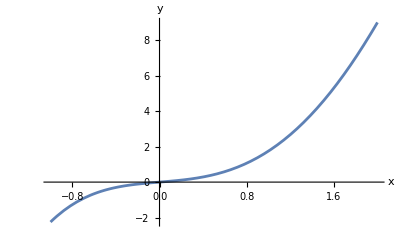

```mathematica
Plot[poly1,{x,-1,2},AxesLabel->{"x","y"}]
```

#### Example: Scatter Plots in Mathematica → ListPlot

In your lab course, you will undoubtedly collect several discrete data sets. Plotting this data will be crucially important to understand if you’ve made any drastic errors in your measurements. You have already imported a data set from the Least Squares Fitting exercise, so we can use that to practice making a scatter plot. ListPlot is the function we need for this, and it takes as input a List of {x,y} pairs.

You already have a list of data points in table1. The “Joined -> True” option can be added AFTER specifying the data in order to connect the points. Follow along with your instructor to create these plots below and compare them.

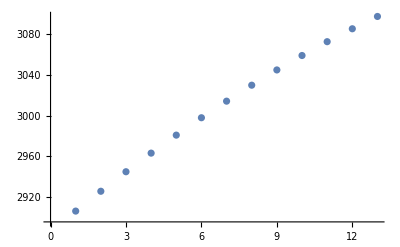

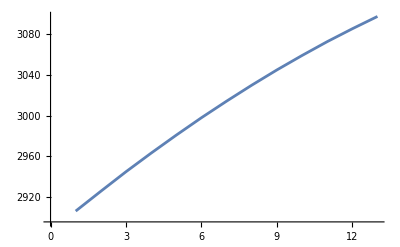

```mathematica
ListPlot[table1]
ListPlot[table1,Joined->True]
```

### Nonlinear Fitting

Mathematica also has the capability to fit arbitrary functions to discrete data. We will utilize this functionality frequently during data analysis in Physical Chemistry labs. Since many of the phenomena we study are inherently nonlinear, we have to move beyond performing a simple linear fit and perform a nonlinear fit instead. In order to perform a nonlinear fit, several ingredients are needed:
1. a list of discrete data points (you already imported them above, table1)
2. an expression that contains the mathematical function you wish to fit. The function should contain at least 1 independent variable, and at least 1 fit parameter. 
3. a list of the fit parameters
4. a list of the independent variables
Work through the following example to fit your first nonlinear function.

#### Example: Create expression for a quadratic function

The simplest nonlinear function we can utilize is a quadratic function:
f(x) = a + b * x + c * x^2
which has one independent variable, x, and 3 fit parameters, {a, b, c}. Follow along with your instructor as they create an expression called quadraticfunc to represent  this equation.

```mathematica
quadraticfunc=a+b*x+c*x^2
```

a+b x+c x^2

#### Example: Fit the quadratic function using NonlinearModelFit

The function which does all the work is called NonlinearModelFit. Follow along with your instructor as they create an expression called nlmfit1 to represent the output of this fit. The arguments of this function are the same ones listed above, or please see the documentation for NonlinearModelFit.

```mathematica
nlmfit1=NonlinearModelFit[table1,quadraticfunc,{a,b,c},x]
```

FittedModel[2885.65+20.8198 x-0.346154 x^2]

#### Example: Extract fit parameters and their errors

Using the argument, “ParameterTable”, you can obtain the fit parameters from the FittedModel as well as their uncertainties. Follow along with your instructor to extract this useful information about your fit. The two columns of particular interest are “Estimate” and “Standard Error”.

```mathematica
nlmfit1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 2885.65 | 0.100637 | 28673.8 | 6.55012×10^-41
b | 20.8198 | 0.0330613 | 629.733 | 2.50893×10^-24
c | -0.346154 | 0.00229792 | -150.638 | 4.08207×10^-18